```mathematica
listk10 ={{8,0.0284630661958965},{10,0.0315480684191363},{12,0.0321746755318005},{14,0.0333638116734364},{16,0.0381281808563128}}
```

{{8,0.0284631},{10,0.0315481},{12,0.0321747},{14,0.0333638},{16,0.0381282}}

```mathematica
listk9 ={{8,0.0478676831160347},{10,0.0612240541302868},{12,0.0647892133888162},{14,0.0702155142853869},{16,0.0737222782883037}}
```

{{8,0.0478677},{10,0.0612241},{12,0.0647892},{14,0.0702155},{16,0.0737223}}

```mathematica
listk8 ={{8,0.0516252298986403},{10,0.0602545074556121},{12,0.085167490759918},{14,0.0933849670857031},{16,0.0979867914922141}}
```

{{8,0.0516252},{10,0.0602545},{12,0.0851675},{14,0.093385},{16,0.0979868}}

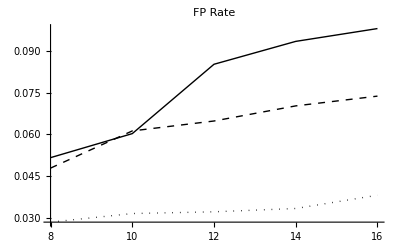

```mathematica
fp =ListPlot[{listk8, listk9,listk10},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"FP Rate",BaseStyle->{FontSize->16}]
```

```mathematica
list10bad={{8,257780},{10,308985},{12,333576},{14,349675},{16,412577}}
```

{{8,257780},{10,308985},{12,333576},{14,349675},{16,412577}}

```mathematica
list9bad={{8,474208},{10,673970},{12,728510},{14,821138},{16,876977}}
```

{{8,474208},{10,673970},{12,728510},{14,821138},{16,876977}}

```mathematica
list8bad={{8,541939},{10,672217},{12,1012438},{14,1156662},{16,1225589}}
```

{{8,541939},{10,672217},{12,1012438},{14,1156662},{16,1225589}}

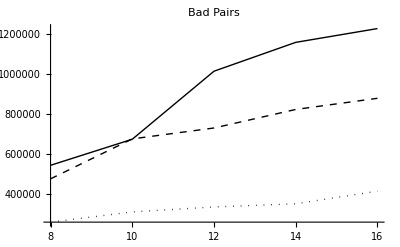

```mathematica
bd = ListPlot[{list8bad, list9bad,list10bad},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Bad Pairs",BaseStyle->{FontSize->16}]
```

```mathematica
list10good={{8,9056649},{10,9794102},{12,10367657},{14,10480667},{16,10820789}}
```

{{8,9056649},{10,9794102},{12,10367657},{14,10480667},{16,10820789}}

```mathematica
list9good={{8,9906642},{10,11008255},{12,11244310},{14,11694538},{16,11895685}}
```

{{8,9906642},{10,11008255},{12,11244310},{14,11694538},{16,11895685}}

```mathematica
list8good={{8,10497561},{10,11156294},{12,11887611},{14,12385955},{16,12507696}}
```

{{8,10497561},{10,11156294},{12,11887611},{14,12385955},{16,12507696}}

```mathematica
lg =LineLegend[{Black,{Black,Dashed},{Black,Dotted}},{"k=8", "k=9","k=10"}]
```

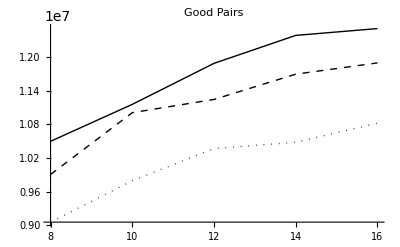

```mathematica
gd = ListPlot[{list8good, list9good,list10good},Joined->True,PlotStyle->{Black,{Black,Dashed},{Black,Dotted}},PlotLabel->"Good Pairs",BaseStyle->{FontSize->16}]
```

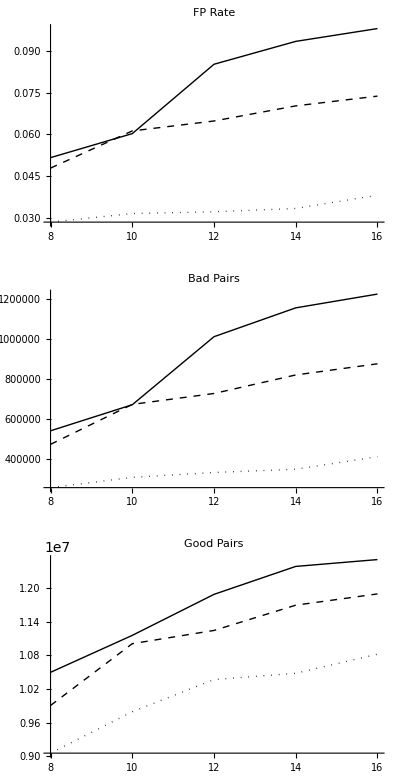

```mathematica
Legended[GraphicsGrid[{{fpl},{bd},{gd}},ImageSize-> Scaled[.5]],lg]
```

```mathematica
Export["edgridn.eps",Legended[GraphicsGrid[{{fp},{bd},{gd}},ImageSize-> Scaled[.5]],lg]]
```

edgridn.eps